## Definitions Section

### Game definitions

```mathematica
(*This commented out version of ma  handles the case where pa= and pb=0. In that case the normal ma is undefined. It doesn't matter, because the condition never happens (they never collaborate) But the division by zero makes mathematica balk.  Uncomment this version if you want to redo the jacobian calculations. *)
(*ma[pa_, pb_, wa_] :=If[pa==1&&pb==0, 0, (wa(1-pa(1-pb)))/(wa(1-pa(1-pb)) + (1-wa)(pa*pb + 0.5(1-pa)pb))]; *)
ma[pa_, pb_, wa_] := (wa(1-pa(1-pb)))/(wa(1-pa(1-pb)) + (1-wa)(pa*pb + 0.5(1-pa)pb)); 
fa[pa_, pb_, wa_] := wa(1-pa(1-pb)) + (1-wa)(pa*pb + (1-pa)pb/2);
fb[pa_,pb_, wa_] := (1-wa)((1-pa)(1-pb) + (1-pa)pb/2);
nobias[epsilon_ , chi_] := (1-epsilon)(1-chi)/(1-epsilon*chi);
firstbias[epsilon_ , chi_] := epsilon(1-chi)/(1-epsilon*chi);
mattbias[epsilon_ , chi_] := (1-epsilon)chi/(1-epsilon*chi);
pia[pa_,pb_, wa_, ba_, bb_, epsilon_, chi_, chat_] := 

(* They collaborate and Adams is first, paper is worth 1 + chat*)
fa[pa, pb, wa](nobias[epsilon, chi]*(ma[pa, pb, wa]*ba +(1-ma[pa, pb, wa])(1-bb)) + firstbias[epsilon, chi])(1+chat) +
(*They collaborate and Babbage is first, papyer is worth 1 + chat *)
 fb[pa,pb, wa]nobias[epsilon,chi](1-bb)(1+chat)  + 
(* They don't collaborate papers are collectively worth 1*)
pa(1-pb)(wa*ba + (1-wa)(1-bb));
pib[pa_, pb_, wa_, ba_, bb_, epsilon_,chi_, chat_] := 
(*They collaborate and Adams is first, paper is worth 1 + chat *)fa[pa,pb,wa](nobias[epsilon,chi]*(ma[pa, pb, wa](1-ba) + (1-ma[pa, pb, wa])bb )+mattbias[epsilon,chi])(1+chat) +
(* They collaborate and Babbage is first, paper is worth 1 + chat *)
fb[pa, pb, wa]*(nobias[epsilon,chi]*bb + firstbias[epsilon,chi] + mattbias[epsilon, chi])(1+chat) + 
(* They don't collaborate, papers are collectively worth 1 *)
pa(1-pb)(wa(1-ba) + (1-wa)bb);
```

### Dynamics definitions

```mathematica
RepA[pa_, pb_, wa_, ba_, bb_,epsilon_,chi_, chat_]:=pa*(pia[1, pb, wa,ba, bb,epsilon,chi,chat] - pia[pa, pb, wa, ba, bb,epsilon,chi,chat]);
RepB[pa_, pb_, wa_, ba_, bb_,epsilon_, chi_, chat_]:=pb*(pib[pa, 1, wa,ba, bb,epsilon,chi, chat] - pib[pa, pb, wa, ba, bb,epsilon,chi,chat]);
```

### Simulations definitions

```mathematica
RepSolve[pastart_, pbstart_, wa_, ba_, bb_, epsilon_, chi_, chat_, time_]:= 
NDSolve[{x'[t] == RepA[x[t], y[t], wa, ba, bb, epsilon,chi, chat], y'[t] ==RepB[x[t],y[t],wa, ba, bb, epsilon,chi, chat], x[0] == pastart, y[0] == pbstart}, {x, y}, {t, 0, time}]
SimRep[nsim_, wa_, ba_, bb_, epsilon_,chi_, chat_, time_] :=Module[{StartingPt, arg,s}, Table[StartingPt = RandomPoint[Cuboid[{0,0}, {1,1}]
, 1];
arg = Join[StartingPt[[1]], {wa,ba, bb, epsilon, chi, chat, time}];
s = Apply[RepSolve, arg];
Evaluate[{x[time], y[time]} /.s][[1]], 
nsim
]];
CountAlph[nsim_] := Count[Map[EuclideanDistance[{1,1}, #] &, nsim], p_/;p<0.01];
CountWork[nsim_] := Count[Map[EuclideanDistance[{0,0}, #] &, nsim], p_/;p<0.01];
```

### Some housekeeping functions

```mathematica
(*The expectation calculations for beta distributions with non-whole number parameters is slow. This allows for caching*)
ClearAll[BaCalc, BbCalc];
BaCalc[alpha_, beta_]:=BaCalc[alpha, beta]=Expectation[ x \[Conditioned] x>=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
BbCalc[alpha_, beta_]:=BbCalc[alpha, beta]=1-Expectation[ x \[Conditioned] x<=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
```

## Analyzing the game

### Looking at payoffs and equilibria

```mathematica
Manipulate[Plot3D[pib[pa, pb, wa, ba, bb,epsilon,chi, chat], {pa, 0,1}, {pb,0,1}, AxesLabel -> {pa, pb, payoff}], {wa, 0.0001, 1}, {ba, 1/2, 1}, {bb, 1/2, 1}, {epsilon,0,1}, {chi, 0, 1},{chat, 0,2}]
```

```mathematica
Manipulate[Plot[pib[0, x, wa, ba, bb,epsilon,chi, chat], {x,0,1}],{wa, 0.0001, 1}, {ba, 1/2, 1}, {bb, 1/2, 1}, {epsilon,0,1}, {chi, 0, 1},{chat, 0, 2}]
```

```mathematica
Reduce[{D[pia[pa,1, wa, ba, bb, 0, 0,chat], pa]==0, 0<=pa<=1, 0<wa<1, wa<ba<1, (1-wa)<bb<1, chat>0}]
```

0≤pa≤1&&0<bb<1&&1-bb<wa<1&&wa<ba<1&&chat>0

```mathematica
Reduce[{D[pib[0,pb, wa, ba, bb, 0, 0, chat], pb]==0, 0<=pa<=1, 0<wa<1, wa<ba<1, (1-wa)<bb<1, chat>0}]
```

0≤pa≤1&&0<bb<1&&1-bb<wa<1&&wa<ba<1&&chat>0

```mathematica
Reduce[{D[pia[pa, 0, wa, ba, bb, epsilon, 0,chat], pa]>0,  0<=pa<=1, 0<wa<1, wa<ba<1, (1-wa)<bb<1, chat>0, 0<= epsilon <= 1}]
```

0<ba<1&&1-ba<bb<1&&1-bb<wa<(-1+bb)/(-2+ba+bb)&&0<epsilon≤1&&0≤pa≤1&&0<chat<(-epsilon+bb epsilon+2 epsilon wa-ba epsilon wa-bb epsilon wa)/(-1+bb+epsilon-bb epsilon+wa-ba wa-bb wa-2 epsilon wa+ba epsilon wa+bb epsilon wa)

```mathematica
Manipulate[Plot[(-epsilon+bb epsilon+2 epsilon wa-ba epsilon wa-bb epsilon wa)/(-1+bb+epsilon-bb epsilon+wa-ba wa-bb wa-2 epsilon wa+ba epsilon wa+bb epsilon wa), {epsilon, 0, 1}, Filling -> Axis], {wa, 0.0001, 1}, {ba, 1/2, 1}, {bb, 1/2, 1}]
```

### Looking at Replicator dynamics

```mathematica
Manipulate[StreamPlot[{RepA[pa,pb, wa,ba, bb,epsilon, chi, chat], RepB[pa,pb, wa,ba, bb, epsilon,chi,chat]}, {pa,0,1}, {pb,0,1}, Frame -> False, Axes->True, AxesOrigin->{0,0},AxesLabel->{"pa", "pb"}], {wa, 0.0001, 1}, {ba, 1/2, 1}, {bb, 1/2, 1}, {epsilon,0,1}, {chi, 0, 1-epsilon},{chat,0,2}]
```

```mathematica
(* Jacobian calculations*)
jack[wa_, ba_, bb_,epsilon_, chi_, chat_] := ({{D[RepA[pa, pb, wa, ba, bb, epsilon, chi, chat], pa], D[RepA[pa,pb, wa, ba, bb, epsilon, chi, chat], pb]}, {D[RepB[pa, pb, wa, ba, bb, epsilon, chi, chat],pa], D[RepB[pa, pb, wa, ba, bb, epsilon, chi, chat],pb]}});
```

```mathematica
stabilityTest[{a_,b_}]:=Which[Re[a]<0&&Re[b]<0,1,Re[a]==0||Re[b]==0,0,True,-1];
```

```mathematica
(* Color Scheme: 
Red: C-Norm stable, I-Norm not
Yellow: I-Norm stable, C-Norm not
Blue: C-Norm stable, I-Norm stable
Green: Non-collaborate stable
White: Something else
*)
colorPoint[wa_, ba_, bb_, epsilon_, chi_, chat_] := Module[{localEigen},
localEigen = Eigenvalues[jack[wa, ba,bb, epsilon, chi, chat]];
If[stabilityTest[localEigen /. {pa -> 1, pb->0}] >0 , 
(*If non-collab is stable*) Green, 
If[stabilityTest[localEigen /.  {pa->0, pb->0}] > 0, 
If[stabilityTest[localEigen /. {pa -> 1, pb->1}] >0,
(*if both stable*) Blue,
(*if only C-Norm, not I-Norm*) Red
], 
(*if C-Norm not stable *)
If[stabilityTest[localEigen /. {pa -> 1, pb->1}] >0,
(*if I-Norm Stable*) Yellow,
(*Neither*)White
]
]
]
];
```

```mathematica
gridSize = 10;
points=Flatten[Table[{epsilon,wa,chat},{epsilon,0,1,1/gridSize},{wa,1/gridSize,1,1/gridSize},{chat,2/gridSize,2,2/gridSize}],2];
args = Flatten[Table[{wa, 0.75, 0.75,epsilon,0, chat},{epsilon,0,1,1/gridSize},{wa,1/gridSize,1,1/gridSize},{chat,2/gridSize,2,2/gridSize}],2];
values = colorPoint @@@ args;
coloredPoints=MapThread[{#1,Point[#2]}&,{values,points}];
Graphics3D[coloredPoints,Axes-> True, AxesLabel->{, , }]
```

-Graphics3D-

```mathematica
gridSize = 10;
points=Flatten[Table[{chi,wa,chat},{chi,0,1,1/gridSize},{wa,1/gridSize,1,1/gridSize},{chat,2/gridSize,2,2/gridSize}],2];
args = Flatten[Table[{wa, 0.75, 0.75,0,chi, chat},{chi,0,1,1/gridSize},{wa,1/gridSize,1,1/gridSize},{chat,2/gridSize,2,2/gridSize}],2];
values = colorPoint @@@ args;
coloredPoints=MapThread[{#1,Point[#2]}&,{values,points}];
Graphics3D[coloredPoints,Axes-> True, AxesLabel->{, , }]
```

-Graphics3D-

## Beta distribution examples

### Illustration

```mathematica
alpha = 5;
beta = 1;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Expectation[ x \[Conditioned] x>=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
localbb = 1- Expectation[ x \[Conditioned] x<=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
Manipulate[StreamPlot[{RepA[pa,pb, localwa,localba, localbb,epsilon, chi, chat], RepB[pa,pb, localwa,localba, localbb, epsilon, chi,chat]}, {pa,0,1}, {pb,0,1}, AxesLabel -> {pa, pb}, Frame->True], {epsilon,0,1},{chi, 0, epsilon}, {chat, 0, 2}]
```

```mathematica
BorderFrame =
Graphics[{
EdgeForm[Thickness[0.005]], FaceForm[],
Rectangle[{0,0}, {1,1}],

Text["Adams", {0.5, -0.1}], 
Text["Babbage", {-0.1, 0.5}, Automatic, {0,1}],

Text["I-Norm", {1.1, 1.1}],
Text["C-Norm", {-0.1, -0.1}]
}];
EqBorderN1 = 
Graphics[{
Thickness[0.02],
Line[{{0,0}, {0,1}, {1,1}}]
}];
EqBorderOtherN = Graphics[{
Thickness[0.02],
Point[{0,0}],
Point[{1,1}]
}];
```

```mathematica
Expectation[ x \[Conditioned] x>=1/2, x \[Distributed]BetaDistribution[8,2]]
1-Expectation[ x \[Conditioned] x<=1/2, x \[Distributed]BetaDistribution[8,2]]
```

1013/1255

14/25

```mathematica
Plot1 = Show[{BorderFrame, EqBorderN1, StreamPlot[{RepA[pa,pb, 0.5,0.75, 0.75,0,0,1], RepB[pa,pb, 0.5,0.75, 0.75, 0,0,1]} // Simplify //Evaluate, {pa,0,1}, {pb,0,1}, Frame -> False, StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot2 = Show[{BorderFrame, EqBorderN1, StreamPlot[{RepA[pa,pb, 8/10,1013/1255, 14/25, 0,0,1], RepB[pa,pb, 8/10,1013/1255, 14/25, 0,0,1] } // Simplify //Evaluate, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot3 = Show[{BorderFrame, EqBorderN1, StreamPlot[{RepA[pa,pb, 2/10,14/25,1013/1255, 0,0,1], RepB[pa,pb, 2/10,14/25,1013/1255, 0,0,1]} // Simplify //Evaluate, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Beta1 = Plot[PDF[BetaDistribution[1,1], x], {x, 0, 1}, Frame-> False, Axes -> True, ImageSize -> Small, Ticks-> None];
Beta2 = Plot[PDF[BetaDistribution[8,2], x], {x, 0, 1}, Frame-> False, Axes -> True, ImageSize -> Small, Ticks-> None];
Beta3 = Plot[PDF[BetaDistribution[2,8], x], {x, 0, 1}, Frame-> False, Axes -> True, ImageSize -> Small, Ticks-> None];
```

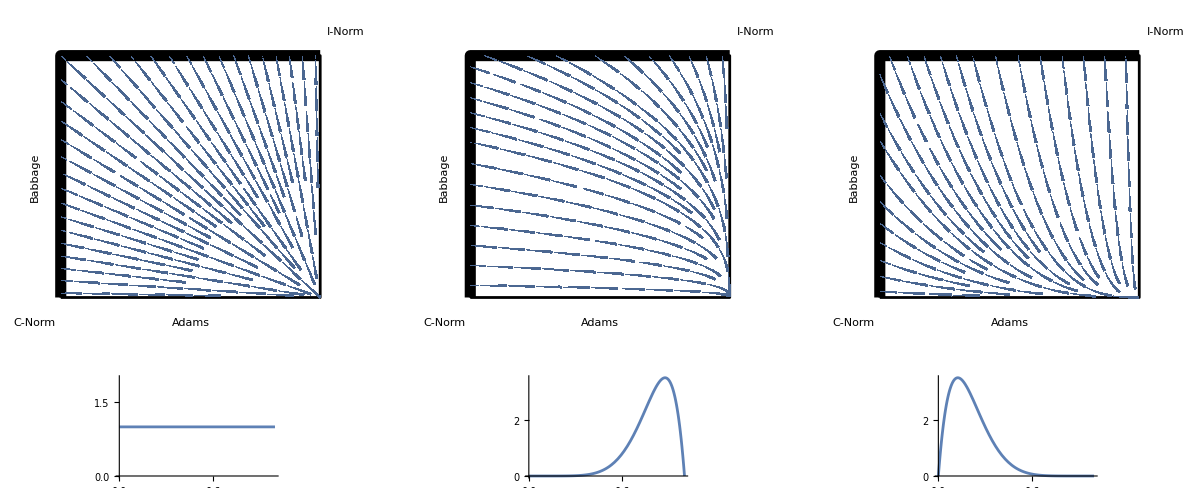

```mathematica
GraphicsGrid[{{Plot1, Plot2, Plot3}, {Beta1, Beta2, Beta3}}]
```

```mathematica
Plot4 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 0.5,0.75, 0.75,1,0,1], RepB[pa,pb, 0.5,0.75, 0.75, 1,0,1]}, {pa,0,1}, {pb,0,1}, Frame -> False, StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot5 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 8/10,1013/1255, 14/25, 1,0,1], RepB[pa,pb, 8/10,1013/1255, 14/25, 1,0,1]}, {pa,0,1}, {pb,0,1}, Frame -> False, StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot6 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 2/10,14/25,1013/1255, 1,0,1], RepB[pa,pb, 2/10,14/25,1013/1255, 1,0,1]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
```

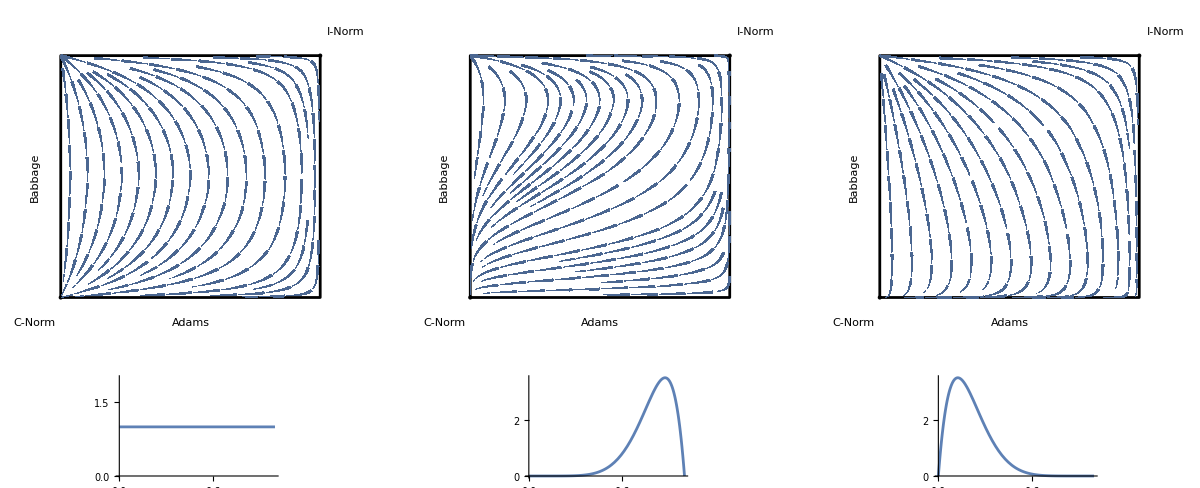

```mathematica
GraphicsGrid[{{Plot4, Plot5, Plot6}, {Beta1, Beta2, Beta3}}]
```

```mathematica
Plot7 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 0.5,0.75, 0.75,0.1,0,1], RepB[pa,pb, 0.5,0.75, 0.75, 0.1,0,1]}, {pa,0,1}, {pb,0,1}, Frame -> False, StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot8 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 8/10,1013/1255, 14/25, 0.1,0,1], RepB[pa,pb, 8/10,1013/1255, 14/25, 0.1,0,1]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot9 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 2/10,14/25,1013/1255, 0.1,0,1], RepB[pa,pb, 2/10,14/25,1013/1255, 0.1,0,1]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot71 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 0.5,0.75, 0.75,0.1,0,0.5], RepB[pa,pb, 0.5,0.75, 0.75, 0.1,0,0.5]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot81 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 8/10,1013/1255, 14/25, 0.1,0,0.5], RepB[pa,pb, 8/10,1013/1255, 14/25, 0.1,0,0.5]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot91 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 2/10,14/25,1013/1255, 0.1,0,0.5], RepB[pa,pb, 2/10,14/25,1013/1255, 0.1,0,0.5]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot72 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 0.5,0.75, 0.75,0.1,0,0.1], RepB[pa,pb, 0.5,0.75, 0.75, 0.1,0,0.1]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot82 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 8/10,1013/1255, 14/25, 0.1,0,0.1], RepB[pa,pb, 8/10,1013/1255, 14/25, 0.1,0,0.1]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
Plot92 = Show[{BorderFrame, EqBorderOtherN, StreamPlot[{RepA[pa,pb, 2/10,14/25,1013/1255, 0.1,0,0.1], RepB[pa,pb, 2/10,14/25,1013/1255, 0.1,0,0.1]}, {pa,0,1}, {pb,0,1}, Frame -> False,StreamMarkers->"Pointer", StreamColorFunction ->None, StreamScale->0.1, StreamPoints ->Medium]}];
```

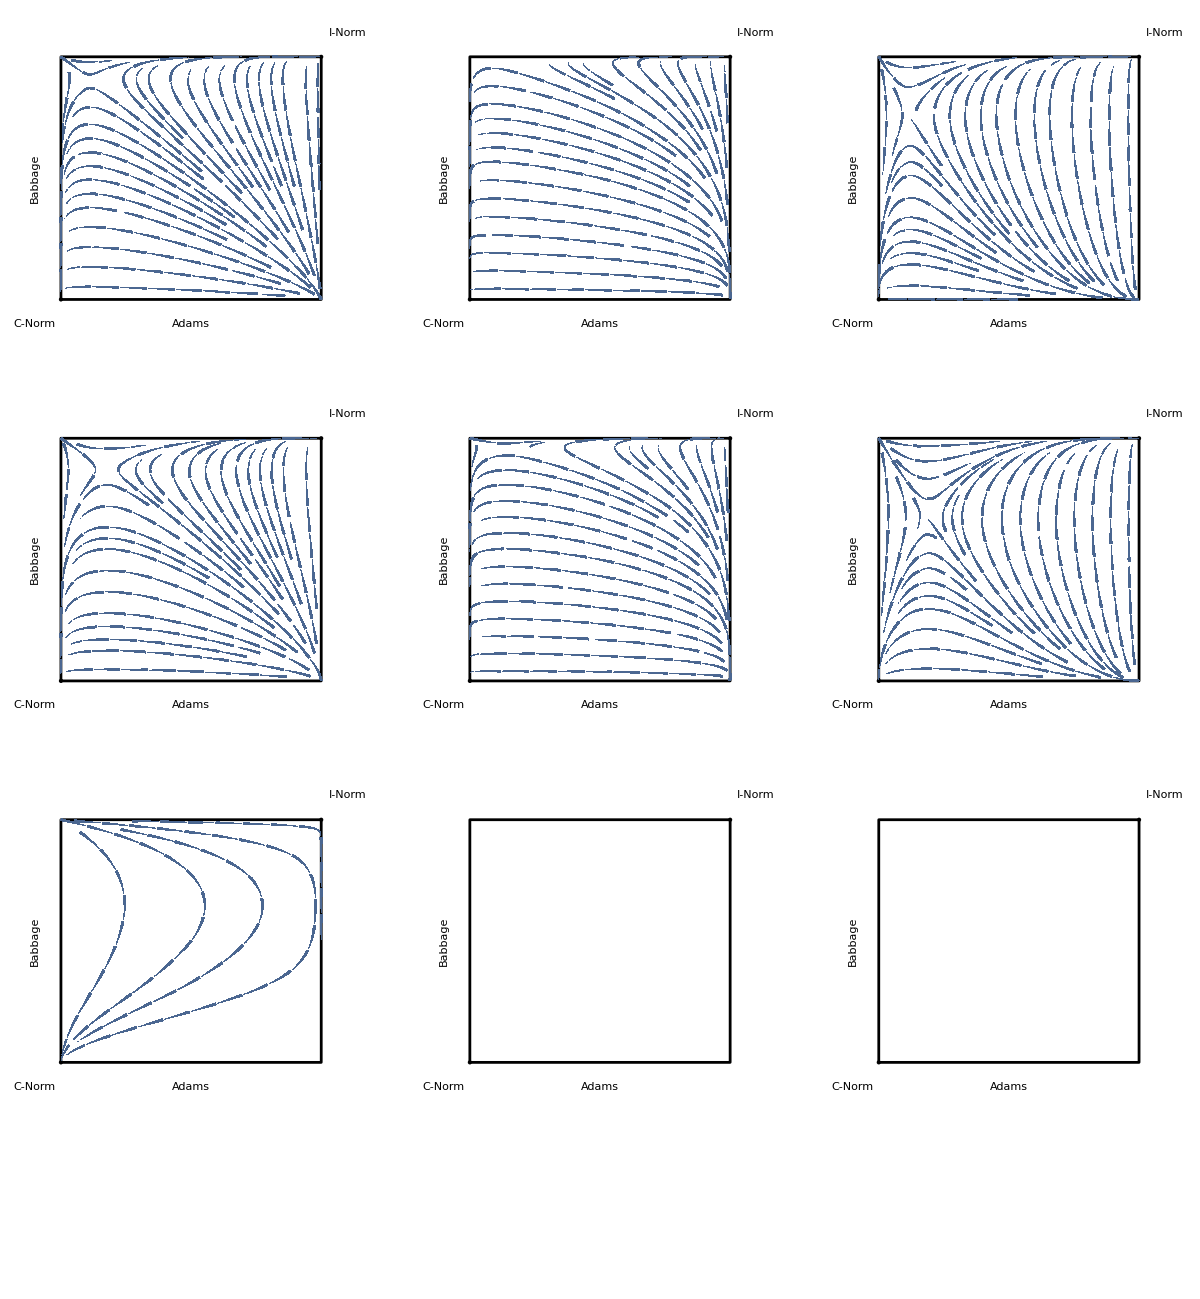

```mathematica
GraphicsGrid[{{Show[Graphics[Text["=1", {-0.1, 0.5}, Automatic, {0,1}],ImageSize->Small]],Plot7, Plot8, Plot9},{Show[Graphics[Text["=0.5", {-0.1, 0.5}, Automatic, {0,1}], ImageSize->Small]],Plot71, Plot81, Plot91}, {Show[Graphics[Text["=0.1", {-0.1, 0.5}, Automatic, {0,1}],ImageSize->Small]], Plot72, Plot82, Plot92}, {Show[Graphics[Text["Dist", {-0.1, 0.5}, Automatic, {0,1}],ImageSize->Small]],Beta1, Beta2, Beta3}}]
```

```mathematica
GraphicsGrid[{{Show[Graphics[Text["", {-0.1, 0.5}, Automatic, {0,1}],ImageSize->Small]],Plot1, Plot2, Plot3},{Show[Graphics[Text["", {-0.1, 0.5}, Automatic, {0,1}], ImageSize->Small]],Plot7, Plot8, Plot9}, {Show[Graphics[Text["", {-0.1, 0.5}, Automatic, {0,1}],ImageSize->Small]], Plot4, Plot5, Plot6}, {Show[Graphics[Text["Dist", {-0.1, 0.5}, Automatic, {0,1}],ImageSize->Small]],Beta1, Beta2, Beta3}}]
```

-Graphics-

### Basin of attraction simulations

#### alpha + beta = 10, chat = 1, epsilon=0.01, chi=0

```mathematica
results = Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = 10-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Expectation[ x \[Conditioned] x>=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
localbb = 1- Expectation[ x \[Conditioned] x<=1/2, x \[Distributed]BetaDistribution[alpha,beta]];
CountAlph[SimRep[1000,localwa, localba, localbb, 0.01,0, 1,10000 ]]/1000], {a, 1, 9}];
expects = Table[alpha = a;
beta = 10-a;
Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]], {a, 1, 9}];
bas =  Table[alpha = a;
beta = 10-a;
 Expectation[ x \[Conditioned] x>=1/2, x \[Distributed]BetaDistribution[alpha,beta]], {a, 1, 9}];
bbs = Table[alpha = a;
beta = 10-a;
 1- Expectation[ x \[Conditioned] x<=1/2, x \[Distributed]BetaDistribution[alpha,beta]], {a, 1, 9}];
```

```mathematica
results
```

{106/125,743/1000,5/8,579/1000,97/200,419/1000,357/1000,251/1000,19/125}

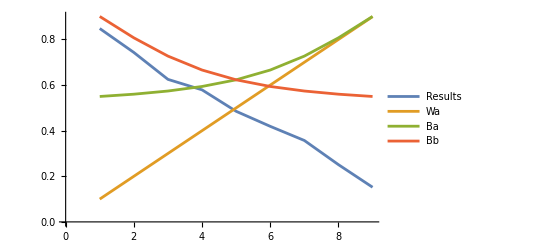

```mathematica
ListLinePlot[{results, expects, bas, bbs}, PlotLegends->{Results, Wa, Ba, Bb}]
```

#### alpha + beta = 100, chat = range from 0 to 1.5, epsilon=0.1, chi=0

```mathematica
gaps = 20;
chatlist = {0, 0.1,0.5,1, 1.5};
total = 100;
sims = 1000;
resultsalpha = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountAlph[SimRep[sims,localwa, localba, localbb, 0.1, 0, chat, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{chat, chatlist}] ;
resultswork = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountWork[SimRep[sims,localwa, localba, localbb, 0.1,0, chat, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{chat, chatlist}] ;
```

NDSolve::ndsz: At t == 14014.7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 57630.4, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 6946.16, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Saving the results so I don't have to rerun this *)
resultsalpha
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{847/1000,767/1000,729/1000,669/1000,61/100,23/40,497/1000,459/1000,56/125,447/1000,79/200,73/200,33/100,57/200,123/500,213/1000,73/500,107/1000,11/200},{891/1000,839/1000,759/1000,143/200,649/1000,291/500,507/1000,249/500,461/1000,113/250,213/500,52/125,347/1000,149/500,34/125,231/1000,183/1000,131/1000,31/500},{112/125,827/1000,191/250,689/1000,639/1000,561/1000,271/500,509/1000,461/1000,221/500,419/1000,49/125,37/100,157/500,34/125,221/1000,81/500,67/500,29/500}}

```mathematica
resultswork
```

{{0,0,0,0,0,0,0,0,0,9/1000,1,1,1,1,1,1,1,1,1},{499/500,1,1,999/1000,1,999/1000,1,1,999/1000,1,1,1,1,1,1,1,1,1,1},{18/125,249/1000,59/200,67/200,51/125,457/1000,97/200,64/125,573/1000,59/100,579/1000,82/125,343/500,691/1000,769/1000,4/5,847/1000,451/500,947/1000},{63/500,197/1000,263/1000,37/125,179/500,429/1000,463/1000,467/1000,521/1000,559/1000,561/1000,629/1000,331/500,86/125,93/125,791/1000,33/40,219/250,951/1000},{13/125,37/200,47/200,331/1000,37/100,371/1000,97/200,487/1000,103/200,129/250,57/100,121/200,63/100,27/40,18/25,381/500,409/500,433/500,471/500}}

```mathematica
gaps = 20;
chatlist = {0, 0.1,0.5,1, 1.5};
total = 100;
sims = 1000;
resultsalpha = {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{847/1000,767/1000,729/1000,669/1000,61/100,23/40,497/1000,459/1000,56/125,447/1000,79/200,73/200,33/100,57/200,123/500,213/1000,73/500,107/1000,11/200},{891/1000,839/1000,759/1000,143/200,649/1000,291/500,507/1000,249/500,461/1000,113/250,213/500,52/125,347/1000,149/500,34/125,231/1000,183/1000,131/1000,31/500},{112/125,827/1000,191/250,689/1000,639/1000,561/1000,271/500,509/1000,461/1000,221/500,419/1000,49/125,37/100,157/500,34/125,221/1000,81/500,67/500,29/500}};
resultswork = {{0,0,0,0,0,0,0,0,0,9/1000,1,1,1,1,1,1,1,1,1},{499/500,1,1,999/1000,1,999/1000,1,1,999/1000,1,1,1,1,1,1,1,1,1,1},{18/125,249/1000,59/200,67/200,51/125,457/1000,97/200,64/125,573/1000,59/100,579/1000,82/125,343/500,691/1000,769/1000,4/5,847/1000,451/500,947/1000},{63/500,197/1000,263/1000,37/125,179/500,429/1000,463/1000,467/1000,521/1000,559/1000,561/1000,629/1000,331/500,86/125,93/125,791/1000,33/40,219/250,951/1000},{13/125,37/200,47/200,331/1000,37/100,371/1000,97/200,487/1000,103/200,129/250,57/100,121/200,63/100,27/40,18/25,381/500,409/500,433/500,471/500}};
```

```mathematica
ListLinePlot[resultsalpha, PlotLegends-> Map[( " =" <> ToString[#])&, chatlist], DataRange -> {1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[resultswork, PlotLegends-> Map[( "" <> ToString[#])&, chatlist], DataRange -> {1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[resultsalpha, PlotLegends-> Map[( " =" <> ToString[#])&, chatlist], DataRange -> {(2/gaps) - 1, 2*(gaps-1)/gaps - 1}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[resultswork, PlotLegends-> Map[( "" <> ToString[#])&, chatlist], DataRange -> {(2/gaps) - 1, 2*(gaps-1)/gaps - 1}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```

-Graphics-

-Graphics-

#### alpha + beta = 100, chat = range from 0.001 to 0.009, epsilon=0.1, chi=0

```mathematica
gaps = 20;
chatlist = {0.001, 0.003,0.005,0.007, 0.009 };
total = 100;
sims = 1000;
resultsalpha = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountAlph[SimRep[sims,localwa, localba, localbb, 0.1,0, chat, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{chat, chatlist}] ;
resultswork = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountWork[SimRep[sims,localwa, localba, localbb, 0.1,0,chat, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{chat, chatlist}] ;
```

```mathematica
resultsalpha
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
resultswork
```

{{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
gaps = 20;
chatlist = {0.001, 0.003,0.005,0.007, 0.009 };
total = 100;
sims = 1000;
resultsalpha = {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
resultswork = {{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1},{3/1000,1/50,437/500,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{499/500,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{999/1000,999/1000,999/1000,1,1,1,1,1,999/1000,1,1,1,1,1,1,1,1,1,999/1000}};
```

```mathematica
ListLinePlot[resultsalpha, PlotLegends-> Map[( " = " <> ToString[#])&, chatlist], DataRange -> {1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[resultswork, PlotLegends-> Map[( "" <> ToString[#])&, chatlist], DataRange -> {1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```

-Graphics-

-Graphics-

#### alpha + beta = 100, chat = 1, epsilon = range from 0.1 to 0.9, chi=0

```mathematica
gaps = 20;
epslist = {0.1,0.2,0.3, 0.4, 0.5};
total = 100;
sims = 1000;
nalpha = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountAlph[SimRep[sims,localwa, localba, localbb, epsilon,0,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{epsilon,epslist}] ;
nwork = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountWork[SimRep[sims,localwa, localba, localbb, epsilon,0,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{epsilon, epslist}] ;
```

```mathematica
nalpha
```

{{221/250,829/1000,151/200,339/500,159/250,119/200,69/125,253/500,47/100,439/1000,423/1000,199/500,357/1000,307/1000,281/1000,109/500,21/125,1/8,63/1000},{421/500,373/500,347/500,307/500,14/25,131/250,443/1000,113/250,107/250,99/250,339/1000,343/1000,309/1000,277/1000,229/1000,23/125,63/500,81/1000,6/125},{729/1000,331/500,593/1000,551/1000,253/500,58/125,52/125,193/500,69/200,317/1000,147/500,34/125,227/1000,27/125,157/1000,33/250,11/100,13/200,3/100},{133/200,589/1000,499/1000,54/125,97/250,351/1000,69/200,59/200,67/250,113/500,53/250,183/1000,41/250,73/500,97/1000,13/125,33/500,27/500,21/1000},{1/250,1/250,1/125,1/200,3/1000,7/1000,1/250,1/100,0,3/500,3/1000,7/1000,9/1000,1/500,7/1000,1/250,1/250,1/100,3/1000}}

```mathematica
nwork
```

{{31/250,87/500,63/250,311/1000,39/100,52/125,479/1000,501/1000,267/500,27/50,577/1000,619/1000,33/50,7/10,717/1000,39/50,169/200,177/200,93/100},{9/50,271/1000,38/125,91/250,449/1000,473/1000,63/125,107/200,583/1000,151/250,157/250,693/1000,699/1000,369/500,791/1000,199/250,859/1000,901/1000,237/250},{1/4,341/1000,201/500,47/100,523/1000,111/200,29/50,123/200,657/1000,351/500,721/1000,709/1000,753/1000,407/500,823/1000,109/125,179/200,921/1000,957/1000},{371/1000,21/50,59/125,273/500,61/100,129/200,339/500,89/125,749/1000,191/250,157/200,201/250,83/100,17/20,847/1000,921/1000,37/40,191/200,971/1000},{299/500,331/500,717/1000,151/200,801/1000,83/100,167/200,173/200,223/250,901/1000,923/1000,459/500,37/40,949/1000,967/1000,973/1000,491/500,197/200,249/250}}

```mathematica
gaps = 20;
epslist = {0.1,0.2,0.3, 0.4, 0.5};
total = 100;
sims = 1000;
nalpha = {{221/250,829/1000,151/200,339/500,159/250,119/200,69/125,253/500,47/100,439/1000,423/1000,199/500,357/1000,307/1000,281/1000,109/500,21/125,1/8,63/1000},{421/500,373/500,347/500,307/500,14/25,131/250,443/1000,113/250,107/250,99/250,339/1000,343/1000,309/1000,277/1000,229/1000,23/125,63/500,81/1000,6/125},{729/1000,331/500,593/1000,551/1000,253/500,58/125,52/125,193/500,69/200,317/1000,147/500,34/125,227/1000,27/125,157/1000,33/250,11/100,13/200,3/100},{133/200,589/1000,499/1000,54/125,97/250,351/1000,69/200,59/200,67/250,113/500,53/250,183/1000,41/250,73/500,97/1000,13/125,33/500,27/500,21/1000},{1/250,1/250,1/125,1/200,3/1000,7/1000,1/250,1/100,0,3/500,3/1000,7/1000,9/1000,1/500,7/1000,1/250,1/250,1/100,3/1000}};
nwork = {{31/250,87/500,63/250,311/1000,39/100,52/125,479/1000,501/1000,267/500,27/50,577/1000,619/1000,33/50,7/10,717/1000,39/50,169/200,177/200,93/100},{9/50,271/1000,38/125,91/250,449/1000,473/1000,63/125,107/200,583/1000,151/250,157/250,693/1000,699/1000,369/500,791/1000,199/250,859/1000,901/1000,237/250},{1/4,341/1000,201/500,47/100,523/1000,111/200,29/50,123/200,657/1000,351/500,721/1000,709/1000,753/1000,407/500,823/1000,109/125,179/200,921/1000,957/1000},{371/1000,21/50,59/125,273/500,61/100,129/200,339/500,89/125,749/1000,191/250,157/200,201/250,83/100,17/20,847/1000,921/1000,37/40,191/200,971/1000},{299/500,331/500,717/1000,151/200,801/1000,83/100,167/200,173/200,223/250,901/1000,923/1000,459/500,37/40,949/1000,967/1000,973/1000,491/500,197/200,249/250}};
```

```mathematica
ListLinePlot[nalpha, PlotLegends-> Map[( "" <> ToString[#])&, epslist], DataRange ->{1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[nwork, PlotLegends-> Map[( "" <> ToString[#])&,epslist], DataRange -> {1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Map[Reverse,nalpha] , PlotLegends-> Map[( "" <> ToString[#])&, epslist], DataRange ->{(2/gaps) - 1, 2*(gaps-1)/gaps - 1}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[Map[Reverse,nwork], PlotLegends-> Map[( "" <> ToString[#])&,epslist], DataRange -> {(2/gaps) - 1, 2*(gaps-1)/gaps - 1}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```

-Graphics-

-Graphics-

#### alpha + beta = 100, chat = 1, epsilon = 0.1, chi=0

```mathematica
gaps = 50;
epslist = {0.1};
total = 100;
sims = 10000;
nalpha = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountAlph[SimRep[sims,localwa, localba, localbb, epsilon,0,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{epsilon,epslist}] ;
nwork = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountWork[SimRep[sims,localwa, localba, localbb, epsilon,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{epsilon, epslist}] ;
```

```mathematica
(* Saved simluation results, so I don't have to rerun the simulation to mess around with the plots*)
```

```mathematica
nalpha
```

{{9259/10000,1801/2000,4339/5000,2091/2500,8091/10000,787/1000,7619/10000,7317/10000,1787/2500,6889/10000,1337/2000,801/1250,6279/10000,6057/10000,5953/10000,709/1250,2753/5000,27/50,1273/2500,631/1250,4909/10000,4789/10000,4667/10000,2269/5000,4561/10000,1099/2500,4297/10000,4141/10000,4173/10000,3907/10000,1869/5000,727/2000,223/625,3311/10000,197/625,182/625,179/625,263/1000,19/80,89/400,2013/10000,1861/10000,209/1250,1383/10000,151/1250,949/10000,89/1250,267/5000,59/2500}}

```mathematica
nwork
```

{{751/10000,1027/10000,1299/10000,827/5000,1871/10000,2147/10000,1197/5000,1293/5000,573/2000,8/25,657/2000,1763/5000,377/1000,1961/5000,83/200,1067/2500,4561/10000,2333/5000,947/2000,501/1000,2501/5000,2617/5000,2691/5000,5447/10000,5473/10000,2833/5000,2863/5000,1173/2000,1503/2500,1519/2500,1251/2000,6299/10000,6527/10000,841/1250,1699/2500,6973/10000,3649/5000,1473/2000,1511/2000,7821/10000,4003/5000,2031/2500,4191/5000,431/500,8813/10000,9081/10000,2321/2500,4761/5000,2431/2500}}

```mathematica
ListLinePlot[nalpha, PlotLegends-> Map[( "n =" <> ToString[#])&, nlist], DataRange ->{1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[nwork, PlotLegends-> Map[( "n =" <> ToString[#])&,nlist], DataRange -> {1/gaps, (gaps-1)/gaps}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Reverse[nalpha[[1]]], PlotLegends-> Map[( "n =" <> ToString[#])&, nlist], DataRange ->{(2/gaps) - 1, 2*(gaps-1)/gaps - 1}, AxesLabel->{"", "Basin of attraction I-Norm"}]
```

-Graphics-

#### alpha + beta = 100, chat = 1, epsilon = 0.1, chi = 0.1 to 0.5

```mathematica
gaps = 20;
chilist = {0.1,0.2,0.3, 0.4, 0.5};
total = 100;
sims = 1000;
nalpha = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountAlph[SimRep[sims,localwa, localba, localbb, 0.1,chi,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{chi,chilist}] ;
nwork = Table[ 
Table[Module[{alpha, beta, localwa, localba, localbb},
alpha = a;
beta = total-a;
localwa = Expectation[x, x \[Distributed]BetaDistribution[alpha,beta]];
localba = Re[BaCalc[alpha,beta]];
localbb = Re[BbCalc[alpha,beta]];
CountWork[SimRep[sims,localwa, localba, localbb, 0.1,chi,1, 100000 ]]/sims], {a, total/gaps, (gaps-1)*total/gaps, total/gaps}], 
{chi, chilist}] ;
```

```mathematica
nalpha
```

{{457/500,817/1000,197/250,93/125,91/125,667/1000,617/1000,287/500,551/1000,53/100,133/250,483/1000,463/1000,447/1000,83/200,67/200,317/1000,141/500,59/250},{907/1000,869/1000,102/125,791/1000,781/1000,96/125,343/500,171/250,649/1000,637/1000,83/125,637/1000,121/200,547/1000,141/250,13/25,59/125,447/1000,199/500},{237/250,179/200,109/125,209/250,409/500,409/500,101/125,391/500,189/250,149/200,189/250,3/4,141/200,177/250,689/1000,159/250,301/500,59/100,567/1000},{239/250,947/1000,463/500,919/1000,114/125,907/1000,111/125,857/1000,871/1000,109/125,427/500,207/250,83/100,811/1000,411/500,791/1000,793/1000,381/500,751/1000},{489/500,122/125,49/50,49/50,973/1000,243/250,483/500,969/1000,487/500,24/25,959/1000,191/200,237/250,191/200,47/50,961/1000,477/500,47/50,189/200}}

```mathematica
nwork
```

{{11/125,33/250,193/1000,27/100,301/1000,321/1000,189/500,101/250,431/1000,469/1000,473/1000,457/1000,141/250,109/200,603/1000,609/1000,133/200,179/250,97/125},{77/1000,129/1000,71/500,39/200,227/1000,11/40,36/125,33/100,333/1000,357/1000,341/1000,2/5,79/200,83/200,229/500,471/1000,501/1000,581/1000,597/1000},{13/250,41/500,23/200,131/1000,169/1000,187/1000,41/200,223/1000,237/1000,259/1000,123/500,139/500,57/200,38/125,309/1000,329/1000,363/1000,51/125,211/500},{9/250,1/20,63/1000,39/500,27/250,12/125,33/250,133/1000,133/1000,16/125,149/1000,153/1000,157/1000,41/250,91/500,189/1000,211/1000,29/125,247/1000},{13/1000,27/1000,37/1000,13/500,9/500,19/1000,7/250,31/1000,13/500,11/250,29/1000,51/1000,53/1000,6/125,51/1000,47/1000,59/1000,1/25,51/1000}}

```mathematica
gaps = 20;
chilist = {0.1,0.2,0.3, 0.4, 0.5};
total = 100;
sims = 1000;
nalpha = {{457/500,817/1000,197/250,93/125,91/125,667/1000,617/1000,287/500,551/1000,53/100,133/250,483/1000,463/1000,447/1000,83/200,67/200,317/1000,141/500,59/250},{907/1000,869/1000,102/125,791/1000,781/1000,96/125,343/500,171/250,649/1000,637/1000,83/125,637/1000,121/200,547/1000,141/250,13/25,59/125,447/1000,199/500},{237/250,179/200,109/125,209/250,409/500,409/500,101/125,391/500,189/250,149/200,189/250,3/4,141/200,177/250,689/1000,159/250,301/500,59/100,567/1000},{239/250,947/1000,463/500,919/1000,114/125,907/1000,111/125,857/1000,871/1000,109/125,427/500,207/250,83/100,811/1000,411/500,791/1000,793/1000,381/500,751/1000},{489/500,122/125,49/50,49/50,973/1000,243/250,483/500,969/1000,487/500,24/25,959/1000,191/200,237/250,191/200,47/50,961/1000,477/500,47/50,189/200}};
nwork = {{11/125,33/250,193/1000,27/100,301/1000,321/1000,189/500,101/250,431/1000,469/1000,473/1000,457/1000,141/250,109/200,603/1000,609/1000,133/200,179/250,97/125},{77/1000,129/1000,71/500,39/200,227/1000,11/40,36/125,33/100,333/1000,357/1000,341/1000,2/5,79/200,83/200,229/500,471/1000,501/1000,581/1000,597/1000},{13/250,41/500,23/200,131/1000,169/1000,187/1000,41/200,223/1000,237/1000,259/1000,123/500,139/500,57/200,38/125,309/1000,329/1000,363/1000,51/125,211/500},{9/250,1/20,63/1000,39/500,27/250,12/125,33/250,133/1000,133/1000,16/125,149/1000,153/1000,157/1000,41/250,91/500,189/1000,211/1000,29/125,247/1000},{13/1000,27/1000,37/1000,13/500,9/500,19/1000,7/250,31/1000,13/500,11/250,29/1000,51/1000,53/1000,6/125,51/1000,47/1000,59/1000,1/25,51/1000}};
```

```mathematica
ListLinePlot[Map[Reverse,nalpha] , PlotLegends-> Map[( "" <> ToString[#])&, chilist], DataRange ->{(2/gaps) - 1, 2*(gaps-1)/gaps - 1}, AxesLabel->{"", "Basin of attraction I-Norm"}]
ListLinePlot[Map[Reverse,nwork], PlotLegends-> Map[( "" <> ToString[#])&,chilist], DataRange -> {(2/gaps) - 1, 2*(gaps-1)/gaps - 1}, AxesLabel->{"", "Basin of attraction C-Norm"}]
```

-Graphics-

-Graphics-